```mathematica
MBN=1;
m=1;
r0=6;
dr0=0;
φ0=0;
dφ0=0.1;
steps=1000;
```

```mathematica
G=1;
c=1;
rs=2*G*MBN/c^2 ;
```

```mathematica
L=dφ0*r0^2*m;
Ene=m*c*Sqrt[dr0^2+(1-rs/r0)*(c^2+(L/(r0*m))^2)];
Eqrad=r''[s]/(1-rs/r[s])-(rs/(2*(r[s]-rs)^2))*(r'[s]^2-(c*Ene)^2)-L^2/r[s]^3==0;
Eqang=φ'[s]==L/(r[s]^2 * m);
```

```mathematica
init={r[0]==r0, r'[0]==dr0, φ[0]==φ0};
sol=NDSolve[
Join[{Eqrad, Eqang}, init],
{r[s], φ[s]},
{s,0, steps},
Method->{"EventLocator","Event":>r[s]-rs,
"EventAction":>Throw[steps=s,"StopIntegration"]}

]
```

{{r[s]→InterpolatingFunction[…][s],φ[s]→InterpolatingFunction[…][s]}}

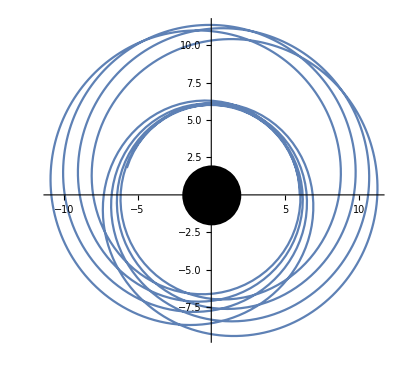

```mathematica
coords=Transpose[{Flatten[Table[φ[s]/.sol, {s, 0, steps}]], Flatten[Table[r[s]/.sol, {s, 0, steps}]]}]; 
ListPolarPlot[coords,PlotRange->All,Epilog->Disk[{0,0},rs],Joined->True]
```

```mathematica
Animate[
ListPolarPlot[
Transpose[{Flatten[Table[φ[s]/.sol,{s, 0, frames}]],Flatten[Table[r[s]/.sol,{s, 0, frames}]]}],
PlotRange->All,
Epilog->Disk[{0,0},rs]
],
{frames, 0, steps},
AnimationRunning->True,
DefaultDuration-> steps/50
]
```